## For one dimensional wavenumber or when qx=qy.Therefore q^2=qx^2+qy^2 and qx=q/(√2)=qy

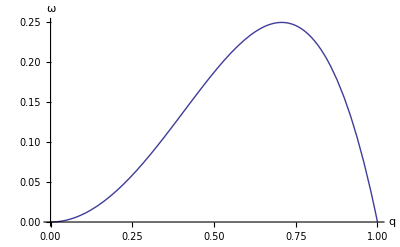

```mathematica
Needs["PlotLegends`"]
(*Growth rate from linear stability h = H(t)Exp(i q X)*)
ω=q^2 A1-q^4 S1;
p1=Plot[{ω/.{A1->1,S1->1}},{q,0,1},PlotRange->{0.5,-0.5},BaseStyle->{FontWeight->"Plain",FontSize->18},AxesLabel->{"q","ω"}
]
```

## When qx≠qy

```mathematica
Clear[qx,qy];
ω2=(qx^2+qy^2) A1-(qx^2+qy^2)^2 S1;
qy= qx;
p2=Plot3D[{ω2/.{A1->1,S1->1}},{qx,0,1},{qy,0,1},
PlotRange->Automatic,BaseStyle->{FontWeight->"Plain",FontSize->18},AxesLabel->{"qx","qy"}]
```

## Full evolution equation with symmetric qx and qy

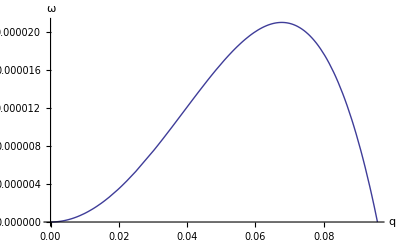

```mathematica
Clear[h,δ,A1,D1,S1,M1,P1,G1,m,E1,λmax,qmax,K1];
h=1;
A1=1;
E1=0.0;
D1=0.001;
S1=100;
δ=E1/(D1 S1);
M1=35.01;
P1=7.02;
G1=1/3;
m=(M1 K1 Bi)/(P1 S1);
a=A1/S1;

xg=1;
Bo=xg*G1/S1;
K1=1;
B=0.0;
Bi=1+B K;

(*The equation below is the maximizing wavenumber. This has been  compared with Oron et al. and Krishnamoorthy et al. and the value matches in all cases.*)

qmax[Bo_,h_]:=Sqrt[(a h^-1-Bo h^3+δ h^3 (Bi h+K1)^-3+m h^2 (Bi h+K1)^-2)/(2 (h^3))];
L=2 π/qmax[Bo,1];

(*Growth rate equation that led to the maximizing wavenumber*)
Clear[h,δ,A1,D1,S1,M1,P1,G1,m,E1,λmax,qmax,K1];
ω3 = Bi ϵ/((Bi h +K1)^2 )- h^3 q^4 -Bo h^2 q^2 + m q^2 h^2/((Bi h + K1)^2) + δ h^3 q^2/((Bi h +K1)^3);
p1=Plot[
ω3/.{Bi->1,h->1,K1->1,Bo->1/300,m->10*0.05,δ->0,ϵ->0.01},
{q,0,1},BaseStyle->{FontWeight->"Plain",FontSize->18},AxesLabel->{"q","ω"},
PlotRange->{0.02,-0.1}
];
p2=Plot[
ω3/.{Bi->1,h->1,K1->1,Bo->1/300,m->1*0.05,δ->0,ϵ->0.0},
{q,0,1},BaseStyle->{FontWeight->"Plain",FontSize->18},AxesLabel->{"q","ω"},
PlotRange->{{0,0.1},{0.0000220069,-0.0}}
]
```

## Full evolution equation with asymmetric qx and qy, qx != qy

```mathematica
Clear[h,δ,A1,D1,S1,M1,P1,G1,m,E1,λmax,qmax,K1];
E1=0.0001;
D1=0.001;
S1=100;
ω4 = Bi ϵ/((Bi h +K1)^2 )- h^3 (qx^2 + qy^2)^2 -Bo h^2 (qx^2 + qy^2) + m (qx^2 + qy^2) h^2/((Bi h + K1)^2) + δ h^3 (qx^2 + qy^2)/((Bi h +K1)^3);
Plot3D[
ω4/.{Bi->1,h->0.2,K1->1,Bo->0/300,m->0.0,δ->E1/(D1 S1),ϵ->E1/S1,qy->2qx},
{qx,0,1},
{qy,0,1},
BaseStyle->{FontWeight->"Plain",FontSize->18},AxesLabel->{"qx","qy"},
PlotRange->{{0,0.1},{0,0.1},{-0.0,0.000001}}
]
```

-Graphics3D-

```mathematica
ω4 = Bi ϵ/((Bi h +K1)^2 )- h^3 (qx^2 + qy^2)^2 -Bo h^2 (qx^2 + qy^2) + m (qx^2 + qy^2) h^2/((Bi h + K1)^2) + δ h^3 (qx^2 + qy^2)/((Bi h +K1)^3)/.{Bi->1, h->1, K1->1, Bo->1/300, m->0.05, δ->0, ϵ->0};
FindMaximum[ω4,{{qx,0,1},{qy,0,1}}]
```

{0.0000210069,{qx→0.0677003,qy→0.}}

```mathematica
e1=0.1;
Manipulate[
Plot3D[
ω4/.{Bi->1,h->1,K1->1,Bo->1/300,m->m1,δ->0,ϵ->e1,qy->2qx},
{qx,0,1},
{qy,0,1},
BaseStyle->{FontWeight->"Plain",FontSize->18},AxesLabel->{"qx","qy"},
PlotRange->{Automatic,Automatic,{-0.4,Full}}
],
{m1,0,10*0.05,0.1}
]
```

## Step Change in thermocapillarity

```mathematica
Clear[h,δ,A1,D1,S1,M1,P1,G1,m,E1,λmax,qmax,K1];

A1=1;
E1=0.0001;
D1=0.001;
S1=100;
δ=E1/(D1 S1);
ϵ=E1/S1;
M1=35.01;
P1=7.02;
G1=1/3;
m=(M1 K1 Bi)/(P1 S1);
a=A1/S1;

xg=1;
Bo=xg*G1/S1;
K1=1;
B=0.0;
Bi=1+B K;
```

```mathematica
ω4 = Bi ϵ/((Bi h +K1)^2 )- h^3 (qx^2 + qy^2)^2 -Bo h^2 (qx^2 + qy^2) + m (qx^2 + qy^2) h^2/((Bi h + K1)^2) + δ h^3 (qx^2 + qy^2)/((Bi h +K1)^3)/.{h->-K1 + Sqrt[(K1 + 1)^2 + Bi ϵ tfac*t]};
```

```mathematica
t=1;
Manipulate[
{Plot3D[
ω4/.{h->-K1 + Sqrt[(K1 + 1)^2 + Bi ϵ tfac*t],qx->1, qy->1},
{qx,0,1},
{qy,0,1},
BaseStyle->{FontWeight->"Plain",FontSize->18},AxesLabel->{"qx","qy"},
PlotRange->{{0,0.1},{0,0.1},{-0.0,5*10^-5}}
],
Plot[-K1 + Sqrt[(K1 + 1)^2 + Bi ϵ tfac],{t,0,t}]
},
{tfac,0,1}
]
```

Plot::plln: Limiting value t in {t, 0, t} is not a machine-sized real number.